```mathematica
Sum[4!/(n!*(4-n)!),{n,0,4}]
```

16

```mathematica
W[n_]:=4!/((4-n)!*n!)
```

```mathematica
{W[0],W[1],W[2],W[3],W[4]}
```

{1,4,6,4,1}

```mathematica
Z[B_]:=6+8*Cosh[2*Em*B]+2*Exp[4*Eps*B]*Cosh[4*Em*B];
```

```mathematica
En[B_]:=-(16*Em*Sinh[2*Em*B]+8*Exp[4*Eps*B]*(Eps*Cosh[4*Em*B]+Em*Sinh[4*Em*B]))/Z[B]
```

```mathematica
{Limit[En[B],B->0],Limit[En[B],B->Infinity]}
```

{-Eps/2,ConditionalExpression[-4 (Em+Eps), Em>0&&Em>2 Eps&&Eps>0]}

```mathematica
S[B_]:=k*(Log[Z[B]]+B*En[B]);
```

```mathematica
{Limit[S[B],B->0],Limit[S[B],B->Infinity]}
```

{k Log[16],ConditionalExpression[0, k∈ℝ&&Em>0&&Em<4 Eps&&Em>2 Eps&&Eps>0]}

```mathematica
(*x=Eps*B , y=Em*B*)
```

```mathematica
Zplot[x_,y_]:=6+8*Cosh[2*y]+2*Exp[4*x]*Cosh[4*y]
```

```mathematica
EnplotB[x_,y_]:=-(16*y*Sinh[2*y]+8*Exp[4*x]*(x*Cosh[4*y]+y*Sinh[4*y]))/Zplot[x,y]  (*EnplotB = En*B*)
```

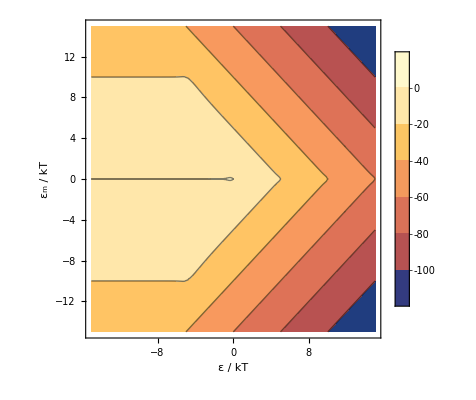

```mathematica
ContourPlot[EnplotB[x,y],{x,-15,15},{y,-15,15},Frame->True,FrameLabel->{Style["ε / kT",Bold,16],Style["εₘ / kT",16,Bold]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotLegends->Automatic]
```

```mathematica
Splotk[x_,y_]:=Log[Zplot[x,y]]+EnplotB[x,y] (*Splotk = S/k*)
```

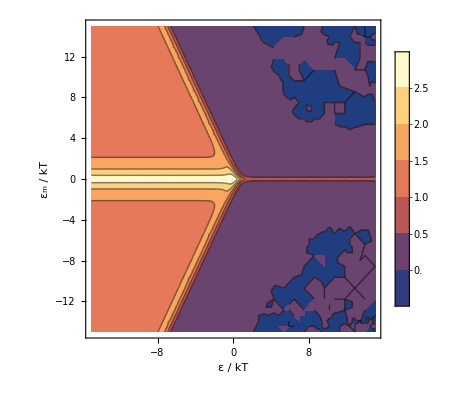

```mathematica
ContourPlot[Splotk[x,y],{x,-15,15},{y,-15,15},Frame->True,FrameLabel->{Style["ε / kT",Bold,16],Style["εₘ / kT",16,Bold]},BaseStyle->{FontFamily->"CambriaMath",FontSize->14},PlotLegends->Automatic]
```

```mathematica
N[Log[16]]
```

2.77259